Simon's Algorithm

Quantum Implementationpaclet:QuantumMob/Q3/tutorial/SimonAlgorithm#1330911220 | Examplespaclet:QuantumMob/Q3/tutorial/SimonAlgorithm#635841546

Simon’s algorithm (Simon, 1997) was the first quantum algorithm featuring an exponential speed-up over the best known classical algorithm for a specific problem. The algorithm is known to have inspired the quantum factorization algorithm. Furthermore, it has recently been shown that Simon’s algorithm can be used to break symmetric-key cryptosystems.

In Simon’s problem, we are given a function f:{0, 1}^n→{0, 1}^n and a secret string s of n bits. For all x,y∈{0,1}^n, f(x)=f(y) if and only if y=x⊕s. Note that f is either one-to-one (s=0) or two-to-one (s≠0). The task is to find the secret string s with as few queries to function f as possible. Classically, one needs queries to f(x) with up to 2^(n-1)+1 different inputs. (More precisely, one needs order of √(2^n) queries to encounter a pair of two bit strings leading to the same result with probability greater than 1/2. The number being √(2^n) rather than 2^n is related to the so-called “birthday paradox”.) Unlike the Deutsch-Jozsa problem, Simon’s problem is known to be hard to solve, even probabilistically.

See also Section 4.2 of the Quantum Workbook (2022)https://doi.org/10.1007/978-3-030-91214-7.

Oraclepaclet:QuantumMob/Q3/ref/OracleQuantumMob Package Symbol | Represents a quantum implementation of classical oracle.
ControlledPowerpaclet:QuantumMob/Q3/ref/ControlledPowerQuantumMob Package Symbol | Controlled exponentiation of a unitary gate

Q3 functions related to Simon's algorithm.

Make sure that the Q3: Symbolic Quantum Simulation package is loaded to use the demonstrations in this documentation:

```mathematica
Needs["QuantumMob`Q3`"]
```

Quantum Implementation

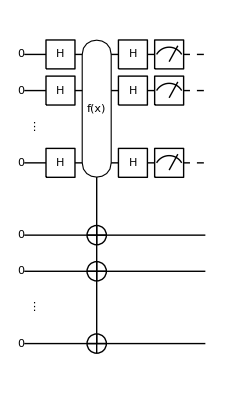

Figure 1. A quantum circuit to implement Simon's algorithm.

The quantum circuit in Figure 1 summarizes Simon’s algorithm. The first Hadamardpaclet:QuantumMob/Q3/ref/HadamardQuantumMob Package Symbol gate on the native register transforms the input state of the whole system as

0⊗0→^(H^(⊗n))1/2^(n/2)Σ_(x=0)^(2^n-1)x⊗0.

The quantum oracle makes a copy of the image f(x) of the state x of the native register to the ancillary register, and leads to

1/2^(n/2)Σ_(x=0)^(2^n-1)x⊗f(x) .

Finally, the second set of Hadamard gates on the native register maps the above state into

Σ_(y=0)^(2^n-1)y⊗1/2^n Σ_(x=0)^(2^n-1)(f(x)(-1))^(x·y) .

The measurement on the native register yields an n-bit string y. The probability for a particular string y is determined by the squared norm, P_y=ψ_yψ_y, of the y-dependent state ψ_y of the ancillary register

ψ_y:=1/2^n Σ_(x=0)^(2^n-1)(f(x)(-1))^(x·y) .

Let us then examine different cases. First, suppose that the secret string s=0. In this case, the function f is one-to-one, and the state ψ_y simply consists of terms that are a rearrangement of the logical basis states

ψ_y:=1/2^n Σ_(z=0)^(2^n-1)(z(-1))^(x·f^-1(z)) ,

where f^-1 is the inverse of f, and hence P_y=2^-n for all y. In other words, for s=0, the measurement produces a random bit string y with uniform probability.

Now, suppose that s≠0. In this case, the function f is two-to-one such that f(x)=f(x⊕s). The terms in state ψ_y appear in pairs giving the same state, f(x)=f(x⊕s). To be more explicit, let ℬ:=f({0,1}^n) be the image of f. Then,

ψ_y:=1/2^n Σ_(z∈ℬ)z{(-1)^(y·a_z)+(-1)^(y·b_z)} ,

where a_z and b_z are the elements in the preimage (or inverse image) of z under f, f(a_z)=f(b_z)=z. Since b_z=a_z ⊕s and (a_z ⊕s)·y = (a_z ·y)⊕(s⊕y), it follows that

{(-1)^(y·a_z)+(-1)^(y·b_z)}=(-1)^(y·a_z){1+(-1)^(y·s)} .

If y·s is odd, that is, y·s=1 (mod 2), then ψ_y is a null vector, and P_y=0 for such a bit string y. On the other hand, if y·s is even, that is, y·s=0 (mod 2), then ψ_y is a finite vector and is independent of y. That is, P_y=2^(1-n) regardless of y as long as y·s is even.

In short, the bit string y resulting from the measurement on the native (first) register always satisfies y·s=0 (mod 2) for any secret bit string s. To find s≡(s_1 s_2(⋯s)_n)_2, one needs to run the algorithms repeatedly to get (n−1) linearly independent bit strings y^(i)≡(y_1^(i)y_1^(i)(⋯y)_n^(i))_2 (i=1,2,. . . ,n − 1), and then solve the set of equations

Σ_(j=1)^n y_j^(i)s_j=0  (mod 2).

It can be argued that the probability to get n−1 linearly independent bit strings out of n runs is slightly larger than 1/4. Therefore, the required number of queries to the quantum oracle is in the order of n, exponentially smaller than for the classical algorithm.

Examples

```mathematica
Needs["QuantumMob`Q3`"]
```

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

### Smaller System

Consider again a secrete bit string:

```mathematica
string={1,1};
```

Consider a two-to-one function obeying the rule (specified in Simon’s problem):

```mathematica
Clear[f];
f[{0,0}]=f[{1,1}]={0,1};
f[{0,1}]=f[{1,0}]={1,1};
```

Here is an implementation of the corresponding quantum oracle:

```mathematica
cc={1,2};
tt={3,4};
all=Join[cc,tt];
qc=QuantumCircuit[Ket[S@all],S[cc,6],Oracle[f,S@cc,S@tt],S[cc,6],Measurement[S[cc,3]]]
```

-Graphics-

```mathematica
out=ExpressionFor[qc]
result=Readout[S[cc,3]]
```

(1_(,,S_(,,1))1_(,,S_(,,2))0_(,,S_(,,3))1_(,,S_(,,4)))/(√2)-(1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4)))/(√2)

{1,1}

```mathematica
mat=Table[ExpressionFor[qc];Readout[S[cc,3]],{2}]
```

{{1,1},{1,1}}

### Larger System

Now, let us examine a lager system. Suppose that we are given a secrete bit string:

```mathematica
string={1,1,0};
```

This is a function consistent with the above secrete bit string:

```mathematica
Clear[f];
f[0]=f[6]=3;
f[1]=f[7]=7;
f[2]=f[4]=4;
f[3]=f[5]=1;
```

Here is an implementation of the corresponding quantum oracle:

```mathematica
cc={1,2,3};
tt={4,5,6};
all=Join[cc,tt];
qc1=QuantumCircuit[Ket[S@all],S[cc,6],Oracle[f,S@cc,S@tt],S[cc,6]];
qc2=QuantumCircuit[qc1,Measurement[S[cc,3]]]
```

-Graphics-

This is one way to get the measurement outcome:

```mathematica
out=ExpressionFor[qc2]
result=Readout[S[cc,3]]
```

1/2 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))0_(,,S_(,,5))1_(,,S_(,,6))+1/2 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))0_(,,S_(,,4))1_(,,S_(,,5))1_(,,S_(,,6))-1/2 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))0_(,,S_(,,5))0_(,,S_(,,6))-1/2 1_(,,S_(,,1))1_(,,S_(,,2))1_(,,S_(,,3))1_(,,S_(,,4))1_(,,S_(,,5))1_(,,S_(,,6))

{1,1,1}

To make repeated measurements, it is more efficient to first compute the state just before the measurement:

```mathematica
new=ExpressionFor[qc1];
```

Now we perform the measurement repeatedly:

```mathematica
data=Table[Measurement[S[cc,3]]@new;Readout[S[cc,3]],{12}];
data//TableForm
```

1 | 1 | 1
1 | 1 | 1
1 | 1 | 0
0 | 0 | 0
0 | 0 | 0
0 | 0 | 1
0 | 0 | 0
0 | 0 | 1
0 | 0 | 0
0 | 0 | 1
1 | 1 | 1
1 | 1 | 1

As two linearly independent vectors (bit strings), we choose these:

```mathematica
mat={{1,1,0},{0,0,1}}
```

{{1,1,0},{0,0,1}}

Then, the linear equation, mat.ss=0 (mod 2), for the Boolean variables ss:={s1,s2,s3} is given by the following, which agrees with the given secrete bit string:

```mathematica
ss={1,1,0}
```

{1,1,0}

```mathematica
Mod[mat.ss,2]
```

{0,0}

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪Quantum Decision Algorithms
▪Quantum Algorithms
▪Quantum Information Systems with Q3

| Related Links
▪D. R. Simon (1997)https://doi.org/10.1137/s0097539796298637,  SIAM Journal on Computing 26, 1474 (1997), "On the Power of Quantum Computation."
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer).